# Setup

```mathematica
(* ================================================================ *)
(* MODULE 0: SETUP                                                  *)
(* ================================================================ *)

baseDir = NotebookDirectory[];
Get[FileNameJoin[{baseDir, "QKT_full.wl"}]];
$HistoryLength = 0;
EnsureDir[dir_] := If[!DirectoryQ[dir],
  CreateDirectory[dir, CreateIntermediateDirectories -> True]];
kStr[k_] := StringReplace[
  If[StringEndsQ[#, "."], # <> "0", #] &[ToString[N[k]]], "." -> "_"];
```

```mathematica
LaunchKernels[14];
```

# Kicked ising

```mathematica
Off[MakeExpression::boxfmt]

(* ============================================================ *)
(*  Mixed-Field Ising Model — Floquet texture test               *)
(* ============================================================ *)

L  = 10;            (* number of spins, dim = 2^L = 1024 *)
J  = 1.0;
hz = 0.8090;        (* Kim-Huse chaotic parameters *)
hx = 0.9045;
tau = 1.0;
dim = 2^L;
```

```mathematica
(* Pauli matrices *)
Id2 = IdentityMatrix[2];
sx  = {{0, 1}, {1, 0}};
sz  = {{1, 0}, {0, -1}};

(* Single-site operator embedded in the L-site space *)
op[mat_, i_, len_] := 
  KroneckerProduct @@ Table[If[k == i, mat, Id2], {k, 1, len}];

(* Diagonal part: Ising + longitudinal field, open BC *)
Hz = -J Sum[op[sz, i, L] . op[sz, i + 1, L], {i, 1, L - 1}]- hz Sum[op[sz, i, L], {i, 1, L}];

(* Off-diagonal part: transverse field *)
Hx = -hx Sum[op[sx, i, L], {i, 1, L}];
```

```mathematica
diagHz   = Normal[Diagonal[Hz]];
expHz    = DiagonalMatrix[Exp[-I tau diagHz]];
sqrtHz   = DiagonalMatrix[Exp[-I tau diagHz/2]];
expHx    = MatrixExp[-I tau Hx];

UF    = expHz . expHx;
UFsym = sqrtHz . expHx . sqrtHz;
```

```mathematica
{eval1, vec1} = Eigensystem[UF];
{eval2, vec2} = Eigensystem[UFsym];
```

```mathematica
vec1[[1]][[1;;-1;;50]]//Im//Chop
```

{0,-0.0158425,0.00725032,0.0112338,0.0326826,-0.00467341,0.00580507,0.0301657,0.00952807,0.0281663,-0.00174744,-0.016399,-0.02115,-0.00370714,0.0054517,0.0446418,-0.00300709,-0.00428922,-0.012649,-0.00434186,0.0233701}

```mathematica
vec2[[1]][[1;;-1;;50]]//Im//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
f1 = ConstantArray[1./Sqrt[dim], dim];

P1 = Abs[vec1 . f1]^2;
P2 = Abs[vec2 . f1]^2;

sat1 = dim * Total[P1^2];
sat2 = dim * Total[P2^2];
```

```mathematica
Print["Asymmetric U_F  :  Σ∞ = ", sat1, "   (expect ~2, CUE-like)"];
Print["Symmetric U_F   :  Σ∞ = ", sat2, "   (expect ~3, COE)"];

(* Optional sanity check: maximum imaginary component of UFsym eigenvectors *)
Print["max |Im(vec_sym)| = ", Max[Abs[Im[vec2]]],
      "   (should be ~ machine epsilon up to a global phase)"];
```

Asymmetric U_F  :  Σ∞ = 6.61063   (expect ~2, CUE-like)

Symmetric U_F   :  Σ∞ = 6.30865   (expect ~3, COE)

max |Im(vec_sym)| = 8.31626×10^-14   (should be ~ machine epsilon up to a global phase)

## Change of basis

```mathematica
gaugeSweep[theta_] := Module[{D, U, V, P},
  D = DiagonalMatrix[Exp[-I theta diagHz]];
  U = D . UFsym . ConjugateTranspose[D];
  V = Eigenvectors[U];
  P = Abs[V . f1]^2;
  dim * Total[P^2]
];
```

```mathematica
sweep = Table[{theta, gaugeSweep[theta]}, {theta, 0, tau/2, tau/40}];
```

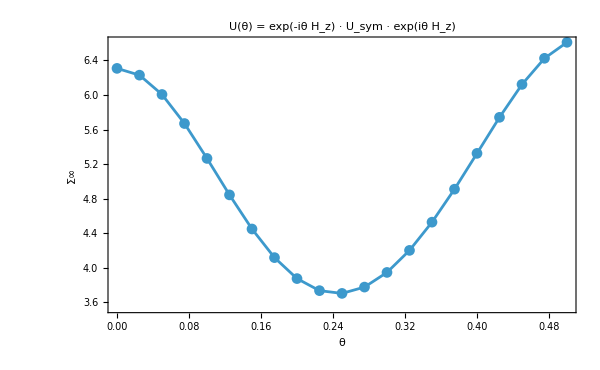

```mathematica
ListLinePlot[sweep,
  PlotMarkers -> Automatic,
  Frame -> True,
  FrameLabel -> {"θ", "Σ∞"},
  GridLines -> {None, {2, 3}},
  PlotRange -> All,
  PlotLabel -> "U(θ) = exp(-iθ H_z) · U_sym · exp(iθ H_z)",
  ImageSize -> 600
]
```

```mathematica
sweep
```

{{0.,6.30865},{0.025,6.23016},{0.05,6.00644},{0.075,5.66978},{0.1,5.26565},{0.125,4.8434},{0.15,4.44837},{0.175,4.11684},{0.2,3.87403},{0.225,3.73431},{0.25,3.70245},{0.275,3.77557},{0.3,3.94543},{0.325,4.2006},{0.35,4.5275},{0.375,4.90947},{0.4,5.3243},{0.425,5.74163},{0.45,6.12286},{0.475,6.42532},{0.5,6.61063}}

## Entanglement

```mathematica
EntanglementEntropySVD[psi_, dA_, dB_] :=
  Module[{mat, sv2},
    mat = ArrayReshape[psi, {dA, dB}];
    sv2 = SingularValueList[mat]^2;
    (* Hard threshold at machine epsilon level *)
    sv2 = Select[sv2, # > 1.*^-14 &];
    (* Renormalize to absorb discarded numerical noise *)
    sv2 = sv2 / Total[sv2];
    -sv2 . Log[sv2]
  ]
```

```mathematica
entanglement=ParallelTable[EntanglementEntropySVD[i, L/2,L/2 ],{i,vec1}];
```

```mathematica
entanglement2=ParallelTable[EntanglementEntropySVD[i, L/2,L/2 ],{i,vec2}];
```

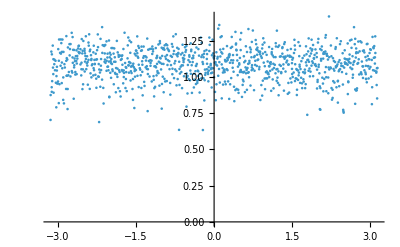

```mathematica
ListPlot[Transpose[{Arg[eval1],entanglement}],PlotRange->All]
```

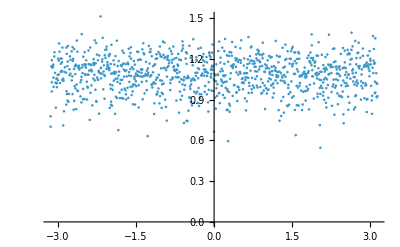

```mathematica
ListPlot[Transpose[{Arg[eval2],entanglement2}],PlotRange->All]
```

```mathematica
PageEntropy[La_,Lb_]:=N[PolyGamma[0,2^La*2^Lb+1]-PolyGamma[0,2^Lb+1]-(2^La-1)/(2*2^Lb)]
```

```mathematica
La=4;
Lb=4;
```

```mathematica
PageEntropy[La,Lb]//N
```

2.27487

```mathematica
Print["dA, dB = ",{2^La,2^Lb}];
Print["Max possible entropy = ",N[Log[Min[2^La,2^Lb]]]];
Print["Page value = ",PageEntropy[La,Lb]];
```

dA, dB = {16,16}

Max possible entropy = 2.77259

Page value = 2.27487

```mathematica
Print["Mean Schmidt rank: ",Mean[Length[Select[SingularValueList[ArrayReshape[#,{2^La,2^Lb}]]^2,#>10^-14&]]&/@vec1]];
```

Mean Schmidt rank: 16

```mathematica
phases=Mod[Arg[eval1],2 Pi];
spacings=Differences[Sort[phases]];
ratios=Min[#1/#2,#2/#1]&@@@Partition[spacings,2,1];
Mean[ratios]
```

0.416354

```mathematica
{J,hz,hx,tau} (*print these to verify*)
```

{1.,0.809,0.9045,1.}

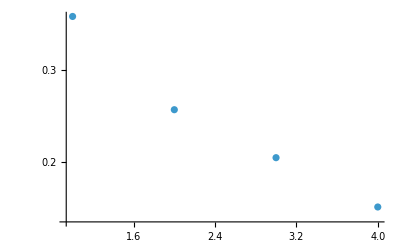

```mathematica
sv=SingularValueList[ArrayReshape[vec1[[1]],{64,64}]];
ListLogPlot[sv^2,PlotRange->All]
```

```mathematica
"C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Spectral measures analysis\\qkt texture.nb"
```

# sectors

```mathematica
(* ============================================================ *)
(*  Reflection-sector diagonalization                            *)
(* ============================================================ *)

(* Build orthonormal bases for P=±1 sectors explicitly *)
buildSectorBases[L_] := Module[
  {dim = 2^L, refl, evenB = {}, oddB = {}, seen, r},
  refl[k_] := FromDigits[Reverse[IntegerDigits[k - 1, 2, L]], 2] + 1;
  seen = ConstantArray[False, dim];
  Do[
    If[! seen[[i]],
     r = refl[i];
     seen[[i]] = True; seen[[r]] = True;
     If[i == r,
      AppendTo[evenB, SparseArray[{i -> 1.}, dim]],
      AppendTo[evenB, SparseArray[{i -> 1./Sqrt[2.], r -> 1./Sqrt[2.]}, dim]];
      AppendTo[oddB,  SparseArray[{i -> 1./Sqrt[2.], r -> -1./Sqrt[2.]}, dim]]
      ]
     ], {i, dim}];
  <|"Even" -> Normal /@ evenB, "Odd" -> Normal /@ oddB|>
];

bases = buildSectorBases[L];
BE = bases["Even"];   (* dE × dim *)
BO = bases["Odd"];    (* dO × dim *)
dE = Length[BE]; dO = Length[BO];

(* Project Floquet operators (basis is real, so Transpose = ConjugateTranspose) *)
UFe  = BE . UF . Transpose[BE];
UFo  = BO . UF . Transpose[BO];
UFse = BE . UFsym . Transpose[BE];
UFso = BO . UFsym . Transpose[BO];

{evalE,  vecE}  = Eigensystem[UFe];
{evalO,  vecO}  = Eigensystem[UFo];
{evalSE, vecSE} = Eigensystem[UFse];
{evalSO, vecSO} = Eigensystem[UFso];

(* Re-expand sector eigenvectors into the full 2^L computational basis *)
vecEfull  = vecE  . BE;
vecOfull  = vecO  . BO;
vecSEfull = vecSE . BE;
vecSOfull = vecSO . BO;
```

```mathematica
La=L/2;
Lb=L/2;
```

```mathematica
(* Sanity checks *)
Print["Sector dims: even = ", dE, ", odd = ", dO, ", total = ", dE + dO];

phasesE = Mod[Arg[evalE], 2 Pi];
ratiosE = Min[#1/#2, #2/#1] & @@@ 
   Partition[Differences[Sort[phasesE]], 2, 1];
Print["<r> in even sector = ", Mean[ratiosE], " (expect ~0.527 for COE)"];
(* Entanglement in even sector *)
entEven = ParallelTable[EntanglementEntropySVD[v, 2^La, 2^Lb], {v, vecEfull}];
Print["Mean entanglement (even sector) = ", Mean[entEven],
      "   Page = ", PageEntropy[La, Lb]];
```

Sector dims: even = 528, odd = 496, total = 1024

<r> in even sector = 0.535225 (expect ~0.527 for COE)

Mean entanglement (even sector) = 2.8794   Page = 2.96631

```mathematica
(* Sanity checks *)
Print["Sector dims: even = ", dE, ", odd = ", dO, ", total = ", dE + dO];
phasesO = Mod[Arg[evalO], 2 Pi];
ratiosO = Min[#1/#2, #2/#1] & @@@ 
   Partition[Differences[Sort[phasesO]], 2, 1];
Print["<r> in even sector = ", Mean[ratiosO], " (expect ~0.527 for COE)"];
(* Entanglement in even sector *)
entOdd = ParallelTable[EntanglementEntropySVD[v, 2^La, 2^Lb], {v, vecSOfull}];
Print["Mean entanglement (odd sector) = ", Mean[entOdd],
      "   Page = ", PageEntropy[La, Lb]];
```

Sector dims: even = 528, odd = 496, total = 1024

<r> in even sector = 0.529176 (expect ~0.527 for COE)

Mean entanglement (odd sector) = 2.88907   Page = 2.96631

```mathematica
(* Compute entanglement for all four sector-operator combinations *)
entUFe  = ParallelTable[EntanglementEntropySVD[v, 2^La, 2^Lb], {v, vecEfull}];
entUFo  = ParallelTable[EntanglementEntropySVD[v, 2^La, 2^Lb], {v, vecOfull}];
entSyme = ParallelTable[EntanglementEntropySVD[v, 2^La, 2^Lb], {v, vecSEfull}];
entSymo = ParallelTable[EntanglementEntropySVD[v, 2^La, 2^Lb], {v, vecSOfull}];

pageVal = PageEntropy[La, Lb];
```

```mathematica
vecEfull[[1]][[1;;-1;;50]]//Im//Chop
vecOfull[[1]][[1;;-1;;50]]//Im//Chop
```

{-0.037416,-0.0000352231,-0.00915363,-0.0203263,-0.0375362,0.0238752,0.0109823,0.0107727,0.0132149,-0.00634075,-0.0211794,0.003023,-0.00391187,0.0487138,0.0440065,0.00866986,0.00716964,-0.00104974,0.00114435,-0.0001929,-0.00540469}

{0,0.00402214,-0.0157498,-0.0234829,0.0108947,0.0109859,0.00601229,0.0651273,-0.0077379,0.000321297,0.0198901,-0.0199474,-0.0296364,0.0207331,-0.00429153,-0.00565369,-0.0249269,0.0281138,0.0210639,-0.00808104,-0.0449846}

```mathematica
vecSEfull[[1]][[1;;-1;;50]]//Im//Chop
vecSOfull[[1]][[1;;-1;;50]]//Im//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

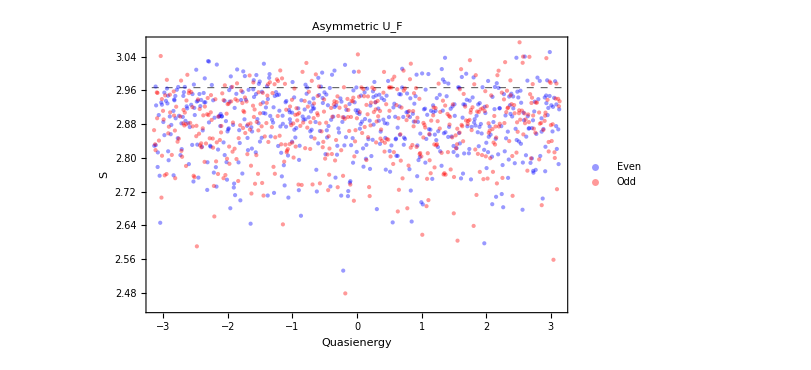

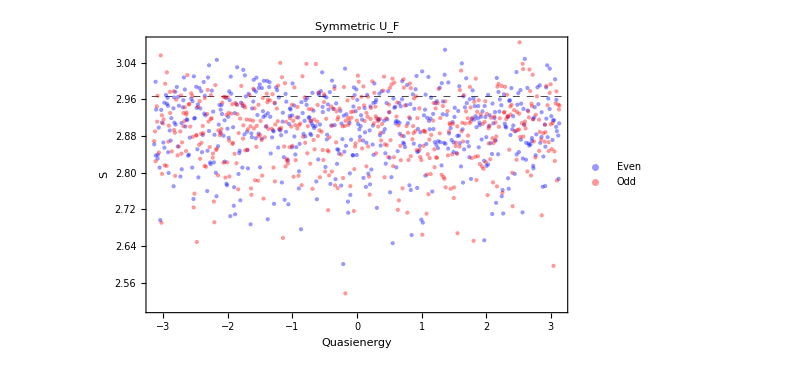

```mathematica
(* Asymmetric UF *)
pUF = ListPlot[
  {Transpose[{Arg[evalE], entUFe}],
   Transpose[{Arg[evalO], entUFo}]},
  PlotRange -> All, Frame -> True,
  FrameLabel -> {"Quasienergy", "S"},
  PlotLegends -> {"Even", "Odd"},
  PlotStyle -> {Directive[Blue, Opacity[0.4], PointSize[0.005]],
                Directive[Red,  Opacity[0.4], PointSize[0.005]]},
  GridLines -> {None, {pageVal}},
  GridLinesStyle -> Directive[Black, Dashed],
  PlotLabel -> Style["Asymmetric U_F", 14, Black],
  ImageSize -> 600
];

(* Symmetric UFsym *)
pSym = ListPlot[
  {Transpose[{Arg[evalSE], entSyme}],
   Transpose[{Arg[evalSO], entSymo}]},
  PlotRange -> All,
 Frame -> True,
  FrameLabel -> {"Quasienergy", "S"},
  PlotLegends -> {"Even", "Odd"},
  PlotStyle -> {Directive[Blue, Opacity[0.4], PointSize[0.005]],
                Directive[Red,  Opacity[0.4], PointSize[0.005]]},
  GridLines -> {None, {pageVal}},
  GridLinesStyle -> Directive[Black, Dashed],
  PlotLabel -> Style["Symmetric U_F", 14, Black],
  ImageSize -> 600
];

pUF
pSym
```

```mathematica
(* ============================================================ *)
(*  Kicked Ising — Ensemble for Texture and SFF                  *)
(* ============================================================ *)

nEns    = 100;
hxCenter = 0.9045;
delta   = 0.005;
hxList  = RandomReal[{hxCenter - delta, hxCenter + delta}, nEns];

(* Build sector bases once — fixed for all realizations *)
bases = buildSectorBases[L];
BE = bases["Even"];
BO = bases["Odd"];
dE = Length[BE];
dO = Length[BO];

(* Uniform textureless state within each sector *)
f1E = ConstantArray[1./Sqrt[dE], dE];
f1O = ConstantArray[1./Sqrt[dO], dO];
```

```mathematica
(* ------------------------------------------------------------ *)
(*  Single-realization eigensystem within sectors               *)
(* ------------------------------------------------------------ *)

GetKIEigensystem[hx_] := Module[
  {Hxloc, expHxloc, UFloc, UFeloc, UFoloc, esE, esO, phE, phO},
  Hxloc    = -hx Sum[op[sx, i, L], {i, 1, L}];
  expHxloc = MatrixExp[-I tau Hxloc];
  UFloc    = expHz . expHxloc;         (* expHz fixed *)
  UFeloc   = BE . UFloc . Transpose[BE];
  UFoloc   = BO . UFloc . Transpose[BO];
  esE = Eigensystem[UFeloc];
  esO = Eigensystem[UFoloc];
  phE = Sort[Mod[Arg[esE[[1]]], 2 Pi]];
  phO = Sort[Mod[Arg[esO[[1]]], 2 Pi]];
  <|"Even" -> <|"Phases" -> phE, "Vectors" -> esE[[2, Ordering[phE]]]|>,
    "Odd"  -> <|"Phases" -> phO, "Vectors" -> esO[[2, Ordering[phO]]]|>|>
];
```

```mathematica
(* ------------------------------------------------------------ *)
(*  Single-realization eigensystem within sectors  SYMMETRIC             *)
(* ------------------------------------------------------------ *)

GetKIEigensystem[hx_] := Module[
  {Hxloc, expHxloc, UFloc, UFeloc, UFoloc, esE, esO, phE, phO},
  Hxloc    = -hx Sum[op[sx, i, L], {i, 1, L}];
  expHxloc = MatrixExp[-I (tau/2) Hxloc];
  UFloc    = expHz . expHxloc.expHz;         (* expHz fixed *)
  UFeloc   = BE . UFloc . Transpose[BE];
  UFoloc   = BO . UFloc . Transpose[BO];
  esE = Eigensystem[UFeloc];
  esO = Eigensystem[UFoloc];
  phE = Sort[Mod[Arg[esE[[1]]], 2 Pi]];
  phO = Sort[Mod[Arg[esO[[1]]], 2 Pi]];
  <|"Even" -> <|"Phases" -> phE, "Vectors" -> esE[[2, Ordering[phE]]]|>,
    "Odd"  -> <|"Phases" -> phO, "Vectors" -> esO[[2, Ordering[phO]]]|>|>
];
```

```mathematica
(* ------------------------------------------------------------ *)
(*  Generate ensemble                                            *)
(* ------------------------------------------------------------ *)

DistributeDefinitions[GetKIEigensystem, buildSectorBases,
  expHz, BE, BO, op, sz, sx, Id2, J, hz, tau, L];

Print["Generating ", nEns, " realizations..."];
rawEns = ParallelTable[GetKIEigensystem[hx], {hx, hxList},
  Method -> "CoarsestGrained"];

(* Structure ensemble per sector *)
kiEnsemble = <|
  "Even" -> Table[<|"Phases" -> d["Even","Phases"],
                    "Vectors" -> d["Even","Vectors"]|>, {d, rawEns}],
  "Odd"  -> Table[<|"Phases" -> d["Odd","Phases"],
                    "Vectors" -> d["Odd","Vectors"]|>, {d, rawEns}]|>;
```

Generating 100 realizations...

```mathematica
(* ------------------------------------------------------------ *)
(*  Texture                                                      *)
(* ------------------------------------------------------------ *)

tMaxTex = 1000;
sigmaSm = 5;

EnsembleTexSector[ensembleList_, f1_, tMax_] := Module[
  {nMat = Length[ensembleList], tGrid = Range[0, tMax], allTex},
  DistributeDefinitions[tGrid, f1];
  allTex = ParallelTable[
    Module[{ph = ensembleList[[i,"Phases"]], vecs = ensembleList[[i,"Vectors"]], 
            d, pArr},
      d = Length[ph];
      pArr = Abs[vecs . f1]^2;
      Table[d * Abs[Total[pArr * Exp[-I t ph]]]^2, {t, tGrid}]
    ], {i, nMat}, Method -> "CoarsestGrained"];
  <|"Time" -> tGrid, "AllTex" -> allTex, "MeanTex" -> Mean[allTex]|>
];

Print["Computing texture — Even sector..."];
texE = EnsembleTexSector[kiEnsemble["Even"], f1E, tMaxTex];
Print["Computing texture — Odd sector..."];
texO = EnsembleTexSector[kiEnsemble["Odd"],  f1O, tMaxTex];

texEsm = Mean[Map[GaussianFilter[#, sigmaSm]&, texE["AllTex"]]];
texOsm = Mean[Map[GaussianFilter[#, sigmaSm]&, texO["AllTex"]]];
```

Computing texture — Even sector...

Computing texture — Odd sector...

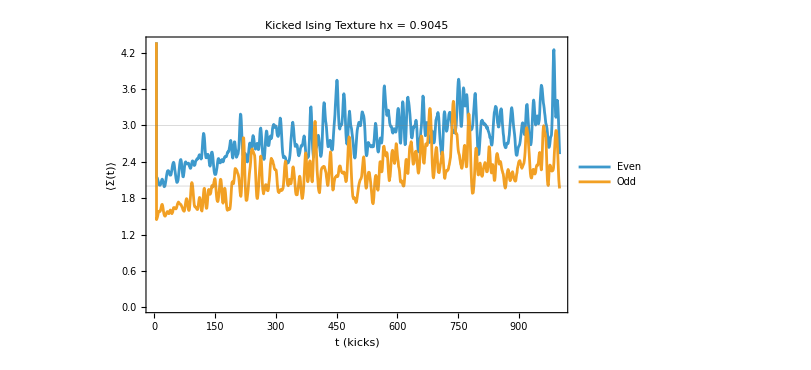

```mathematica
ListLinePlot[
  {Transpose[{texE["Time"], texEsm}],
   Transpose[{texO["Time"], texOsm}]},
  PlotLegends -> {"Even", "Odd"},
  FrameLabel -> {"t (kicks)", "⟨Σ(t)⟩"},
  GridLines -> {None, {2, 3}},
  Frame -> True, ImageSize -> 600,
  PlotLabel -> Style["Kicked Ising Texture  hx = " <> ToString[hxCenter], 14]
]
```

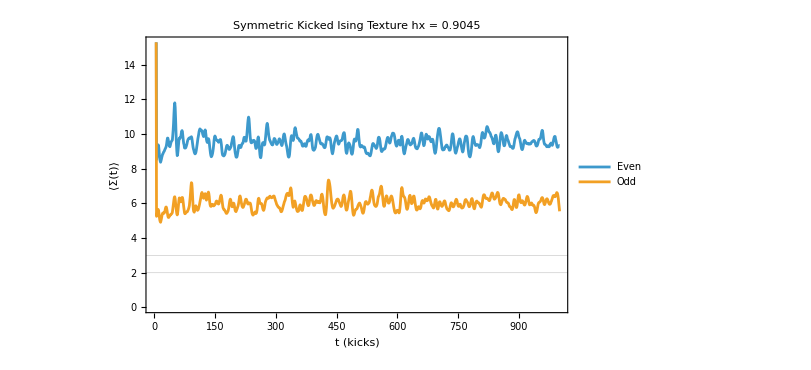

```mathematica
ListLinePlot[
  {Transpose[{texE["Time"], texEsm}],
   Transpose[{texO["Time"], texOsm}]},
  PlotLegends -> {"Even", "Odd"},
  FrameLabel -> {"t (kicks)", "⟨Σ(t)⟩"},
  GridLines -> {None, {2, 3}},
  Frame -> True, ImageSize -> 600,
  PlotLabel -> Style["Symmetric Kicked Ising Texture  hx = " <> ToString[hxCenter], 14]
]
```

```mathematica
(* ------------------------------------------------------------ *)
(*  Spectral Form Factor                                         *)
(* ------------------------------------------------------------ *)

tauMax = 1.0;
nPts   = 2000;

kiSpectraE = Table[
  UnfoldLinear[kiEnsemble["Even"][[i, "Phases"]]], {i, nEns}];
kiSpectraO = Table[
  UnfoldLinear[kiEnsemble["Odd"][[i,  "Phases"]]], {i, nEns}];

sffE = EnsembleSFF[kiSpectraE, tauMax, nPts];
sffO = EnsembleSFF[kiSpectraO, tauMax, nPts];
```

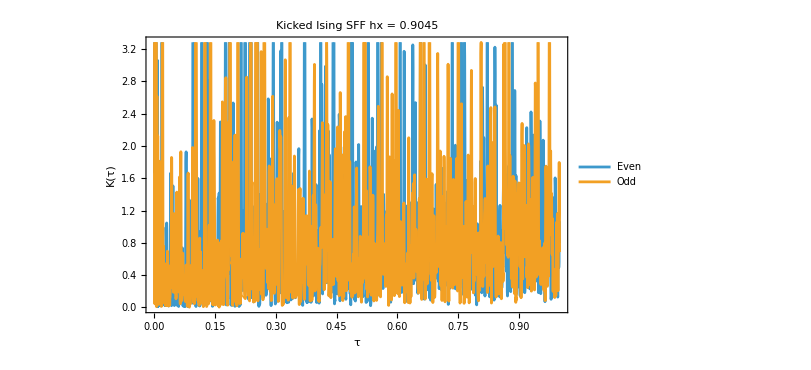

```mathematica
ListPlot[
  {Transpose[{sffE["Tau"], sffE["MeanK"]}],
   Transpose[{sffO["Tau"], sffO["MeanK"]}]},
  PlotLegends -> {"Even", "Odd"},
  FrameLabel -> {"τ", "K(τ)"},
  Frame -> True, ImageSize -> 600,
Joined->True,
  PlotLabel -> Style["Kicked Ising SFF  hx = " <> ToString[hxCenter], 14]
]
```

```mathematica
(* EnsembleSFFFull: identical to library EnsembleSFF but keeps all realizations *)
EnsembleSFFFull[spectraList_List, tauMax_Real, nPts_Integer] :=
  Module[{nMat, taus, specArray, allK},
    nMat = Length[spectraList];
    taus = N[Range[1, nPts] (tauMax/nPts)];
    specArray = Map[#["Spectrum"] &, spectraList];
    DistributeDefinitions[CompileSFF, taus, specArray];
    allK = ParallelTable[CompileSFF[specArray[[i]], taus],
      {i, nMat}, Method -> "CoarsestGrained"];
    <|"Tau" -> taus, "AllK" -> allK,
      "MeanK" -> Mean[allK],
      "SE"    -> StandardDeviation[allK]/Sqrt[nMat*1.]|>];

(* SmoothSFF: Gaussian filter with sigma in tau units *)
SmoothSFF[k_, tau_, sigma_] := Module[{dt, n},
  dt = (Last[tau] - First[tau])/(Length[tau] - 1);
  n  = Max[1, Round[sigma/dt]];
  GaussianFilter[k, n]];
```

```mathematica
(* Build unfolded spectra from kicked Ising ensemble *)
kiSpectraEven = Table[
  UnfoldLinear[kiEnsemble["Even"][[i, "Phases"]]], {i, nEns}];
kiSpectraOdd = Table[
  UnfoldLinear[kiEnsemble["Odd"][[i,  "Phases"]]], {i, nEns}];
```

```mathematica
(* Now the QKT workflow applies directly *)
tauMaxSFF = 3.0;
nPtsSFF   = 10000;
sigmaSm   = 0.01;

sffEven = EnsembleSFFFull[kiSpectraEven, tauMaxSFF, nPtsSFF];
sffOdd  = EnsembleSFFFull[kiSpectraOdd,  tauMaxSFF, nPtsSFF];

tauGrid = sffEven["Tau"];

kEvenAllSm = Map[SmoothSFF[#, tauGrid, sigmaSm] &, sffEven["AllK"]];
kOddAllSm  = Map[SmoothSFF[#, tauGrid, sigmaSm] &, sffOdd["AllK"]];
kEvenMeanSm = Mean[kEvenAllSm];
kOddMeanSm  = Mean[kOddAllSm];
kCOEAn = Map[COESFFAnalytical, tauGrid];
```

CompiledFunction::cfta: Argument {0.0160726,0.0281185,0.0363576,0.0431591,0.0461552,0.0507091,0.0659482,0.115265,0.115848,0.118142,0.130229,0.131927,0.154495,«25»,0.474623,0.525701,0.536547,0.537937,0.54918,0.562317,0.564142,0.571727,0.57834,0.58338,0.587507,0.603953,«478»}[Spectrum] at position 1 should be a rank 1 tensor of machine-size real numbers.

CompiledFunction::cfta: Argument {0.0141458,0.0255056,0.0381347,0.0440757,0.0445056,0.0530751,0.0641471,0.114168,0.116264,0.118833,0.127061,0.129664,0.155237,«25»,0.47762,0.524525,0.536206,0.539801,0.548182,0.563147,0.563399,0.569616,0.581402,0.582116,0.590308,0.602114,«478»}[Spectrum] at position 1 should be a rank 1 tensor of machine-size real numbers.

CompiledFunction::cfta: Argument {0.016034,0.0280662,0.0363933,0.0431774,0.0461221,0.0507566,0.065912,0.115285,0.115815,0.118156,0.130166,0.131882,0.15451,«25»,0.474683,0.525678,0.536612,0.537902,0.54916,0.562334,0.564127,0.571684,0.578401,0.583354,0.587563,0.603916,«478»}[Spectrum] at position 1 should be a rank 1 tensor of machine-size real numbers.

CompiledFunction::cfta: Argument {0.0144098,0.0258642,0.0378914,0.0439499,0.0447315,0.0527507,0.0643935,0.114399,0.116127,0.118738,0.127496,0.129973,0.155135,«25»,0.477209,0.524687,0.536443,0.539355,0.548319,0.563034,0.5635,0.569905,0.580983,0.582288,0.589924,0.602366,«478»}[Spectrum] at position 1 should be a rank 1 tensor of machine-size real numbers.

CompiledFunction::cfta: Argument {0.0138442,0.0250958,0.0384124,0.044215,0.0442522,0.0534459,0.0638657,0.113904,0.116421,0.11894,0.126565,0.129311,0.155353,«25»,0.47809,0.524341,0.535935,0.54031,0.548026,0.563275,0.563284,0.569285,0.581855,0.581944,0.590747,0.601826,«478»}[Spectrum] at position 1 should be a rank 1 tensor of machine-size real numbers.

General::stop: Further output of Argument `1` at position `2` should be a rank `3` tensor of `4`s. will be suppressed during this calculation.

General::stop: Further output of CompiledFunction::cfta will be suppressed during this calculation.

General::stop: Further output of Further output of `1` will be suppressed during this calculation. will be suppressed during this calculation.

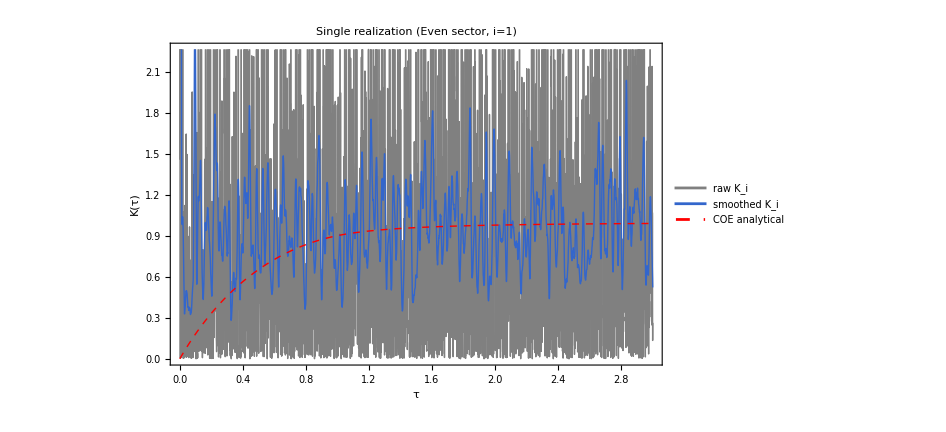

```mathematica
iShow = 1;

plotIndiv = ListLinePlot[
  {Transpose[{tauGrid, sffEven["AllK"][[iShow]]}],
   Transpose[{tauGrid, kEvenAllSm[[iShow]]}],
   Transpose[{tauGrid, kCOEAn}]},
  PlotStyle -> {Directive[Thin, Gray],
                Directive[Thick, RGBColor[0.2, 0.4, 0.8]],
                Directive[Thick, Dashed, Red]},
  PlotLegends -> {"raw K_i", "smoothed K_i", "COE analytical"},
  Frame -> True,
  FrameLabel -> {"τ", "K(τ)"},
  PlotLabel -> "Single realization (Even sector, i=" <> ToString[iShow] <> ")",
  ImageSize -> 700]
```

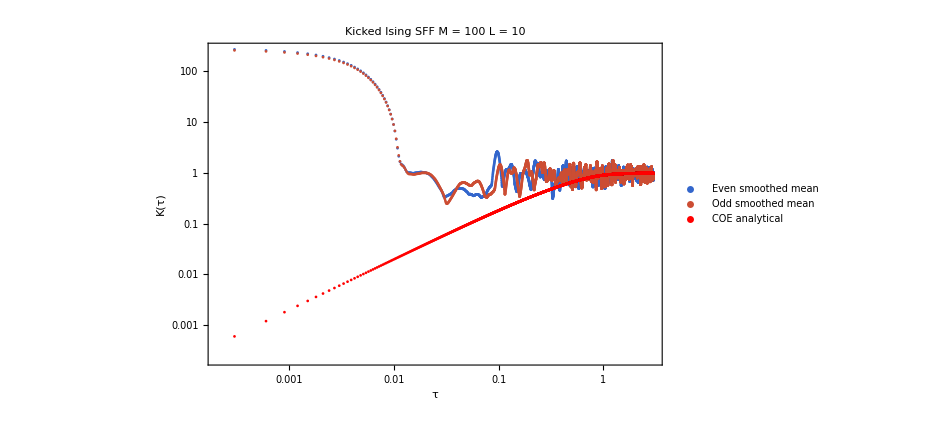

```mathematica
plotEnsemble = ListLogLogPlot[
  {Transpose[{tauGrid, kEvenMeanSm}],
   Transpose[{tauGrid, kOddMeanSm}],
   Transpose[{tauGrid, kCOEAn}]},
  PlotStyle -> {Directive[Thick, RGBColor[0.2, 0.4, 0.8]],
                Directive[Thick, RGBColor[0.8, 0.3, 0.2]],
                Directive[Thick, Dashed, Red]},
  PlotLegends -> {"Even smoothed mean", "Odd smoothed mean", "COE analytical"},
  Frame -> True,
  FrameLabel -> {"τ", "K(τ)"},
  PlotLabel -> "Kicked Ising SFF  M = " <> ToString[nEns] <>
               "  L = " <> ToString[L],
  LabelStyle -> Directive[Black, 20],
  ImageSize -> 700]
```

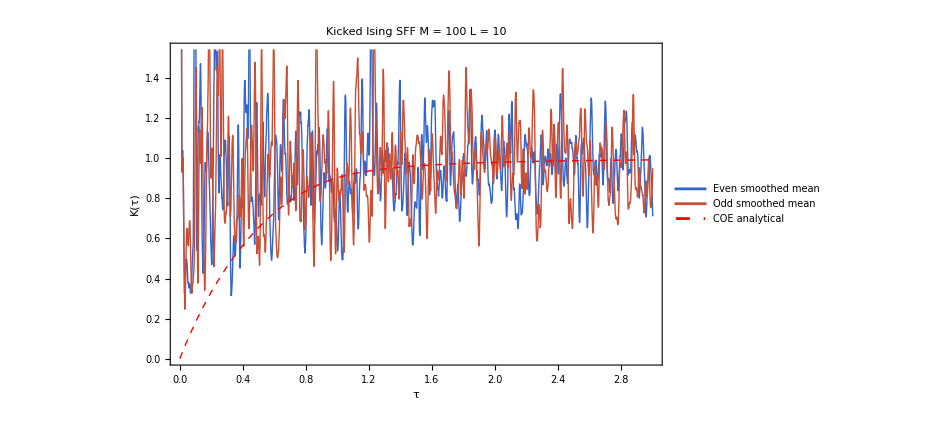

```mathematica
plotEnsemble = ListLinePlot[
  {Transpose[{tauGrid, kEvenMeanSm}],
   Transpose[{tauGrid, kOddMeanSm}],
   Transpose[{tauGrid, kCOEAn}]},
  PlotStyle -> {Directive[Thick, RGBColor[0.2, 0.4, 0.8]],
                Directive[Thick, RGBColor[0.8, 0.3, 0.2]],
                Directive[Thick, Dashed, Red]},
  PlotLegends -> {"Even smoothed mean", "Odd smoothed mean", "COE analytical"},
  Frame -> True,
  FrameLabel -> {"τ", "K(τ)"},
  PlotLabel -> "Kicked Ising SFF  M = " <> ToString[nEns] <>
               "  L = " <> ToString[L],
  LabelStyle -> Directive[Black, 20],
  ImageSize -> 700]
```